## Généralités

```mathematica
(* matrice de transfert d'un site au suivant *)
M[tr_,tl_,e_]:={{e/tr,-tl/tr},{1,0}};
(* matrice de transfert de la 2-molécule *)
M1=M[1,v,e].M[v,1,e];
%//MatrixForm
```

(e^2/v-v | -e/v
e/v | -1/v)

```mathematica
(* matrice de transfert de la 4-molécule *)
M1/.v->r v;
%.M1//Expand;
M2=%
```

{{-e^2/r-e^2 r-e^2/(r v^2)+e^4/(r v^2)+r v^2,e r+e/(r v^2)-e^3/(r v^2)},{-e/r-e/(r v^2)+e^3/(r v^2),1/(r v^2)-e^2/(r v^2)}}

```mathematica
(* couplages renormalisés *)
vv=(r v^2)/(e^2-1);
e1=e(1-r^-1 vv);
e2=e(1-r vv);
(* la 4-molécule correspond bien à une 2-molécule avec les couplages renormalisés *)
M[1,vv,e2].M[vv,1,e1];
%//Expand//Simplify;
%==Simplify[M2]
```

True

## Molécules isolées

#### Intro

```mathematica
(* matrice de transfert de la 2-molécule *)
M1=M[1,v,e].M[v,1,e];
M1//MatrixForm
```

(e^2/v-v | -e/v
e/v | -1/v)

```mathematica
(* hamiltonien dans la base atomique *)
h4={{0,1,0,0},{1,0,v,0},{0,v,0,1},{0,0,1,0}};
%//MatrixForm
```

(0 | 1 | 0 | 0
1 | 0 | v | 0
0 | v | 0 | 1
0 | 0 | 1 | 0)

Dans le cas d’une molécule isolée on a des conditions aux limites nulles. Cela donne pour la fonction d’onde d’énergie E dont les coefficients sont les ψ_i dans la base atomique les conditions :
E ψ_0 = t_(0,1) ψ_1
E ψ_N= t_(N,N-1) ψ_(N-1) 
Dans la suite on suppose t_(0,1)=t_(N,N-1)=1. C’est de toute façon le cas pour nos molécules.
On peut grâce à la condition aux limites au bord gauche choisir (ψ_1, ψ_0) = (E, 1). Le vecteur propre ne sera alors pas normalisé, mais peu importe. 
Appelons M la matrice de transfert qui va d’un bord à l’autre du système, ie celle qui donne :
M (ψ_1, ψ_0) = (ψ_N, ψ_(N-1))
Après application de M sur (ψ_1, ψ_0), on obtient ψ_N comme un polynôme de degré N-1 en E. Grâce à la condition aux limites au bord droit on obtient une équation polynomiale de degré N à résoudre, qui nous donne les N énergies propres du système.

```mathematica
M1.{e ,1}//Expand;
spec4=Solve[e*%[[1]]==%[[2]],e]
(* les énergies obtenues sont bien celles de la 4-molécule *)
Eigenvalues[h4]
```

{{e→1/2 (-v-√(4+v^2))},{e→1/2 (v-√(4+v^2))},{e→1/2 (-v+√(4+v^2))},{e→1/2 (v+√(4+v^2))}}

{1/2 (-v-√(4+v^2)),1/2 (v-√(4+v^2)),1/2 (-v+√(4+v^2)),1/2 (v+√(4+v^2))}

La matrice de transfert nous donne aussi les vecteurs propres.

```mathematica
Block[
{i=4,vp},
vp={1,e ,(M1.{e ,1})[[2]],(M1.{e ,1})[[1]]}/.spec4[[i]];
Print[vp//Expand];
((e/.spec4[[i]])^-1*h4.vp)//FullSimplify//Expand
]
```

{1,v/2+(√(4+v^2))/2,v/2+(√(4+v^2))/2,1}

{1,v/2+(√(4+v^2))/2,v/2+(√(4+v^2))/2,1}

### Spectre

#### Avec une matrice de transfert

```mathematica
(* matrice de transfert de la 4-molécule *)
Clear[M];
M[v_]:={{e^2/v-v,-e/v},{e/v,-1/v}};
```

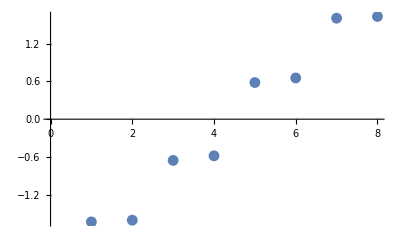

```mathematica
ClearAll[M,vv];
M[vv_]:={{e^2/vv-vv,-e/vv},{e/vv,-1/vv}};
ClearAll[r,v];
Block[{iter=1,v=1.,r=0.1,mf,transl,spec},
mf=Nest[{Expand[1/2#[[1]].(M[r^(#[[2]]) v]).#[[1]]],#[[2]]+1}&,{1/2 M[v],1},iter][[1]];
transl=mf.{e ,1};
spec=NSolve[e*transl[[1]]==transl[[2]],e];
ListPlot[e/.spec]
]
```

#### Diagonalisation directe

```mathematica
(* amplitude de saut entre les sites atomiques i et i+1 *)
Clear[t];
t[i_]:=Block[{k,tt},
k=IntegerExponent[i,2];
If[k==0,tt=1,tt=v r^(k-1)];
tt]
```

```mathematica
(* hamiltonien avec conditions aux bords nulles *)
Clear[h];
h[n_]:=Block[{tbl,ar},
tbl=Table[{i,i+1}->t[i],{i,1,2^n-1}];
ar=SparseArray[tbl,{2^n,2^n}];
ar+Transpose[ar]
]
```

```mathematica
h[4]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | v | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | v | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | r v | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | r v | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | v | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | v | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | r^2 v | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | r^2 v | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | v | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | r v | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r v | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | v | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | v | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

Eigenvalues::arh: Because finding 512 out of the 512 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

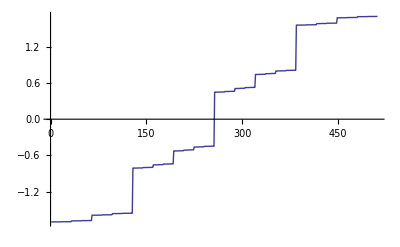

```mathematica
(* spectre *)
Block[{v=1.,r=.4,vp},
vp=Sort[Eigenvalues[h[9]]];
ListPlot[vp,Joined->True]
]
```

```mathematica
Block[{v=.3,r=.3},
Eigensystem[h[2]]]
```

{{1.16119,-1.16119,0.861187,-0.861187},{{0.461427,0.535803,0.535803,0.461427},{-0.461427,0.535803,-0.535803,0.461427},{0.535803,0.461427,-0.461427,-0.535803},{0.535803,-0.461427,-0.461427,0.535803}}}

Eigensystem::arh: Because finding 2048 out of the 2048 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

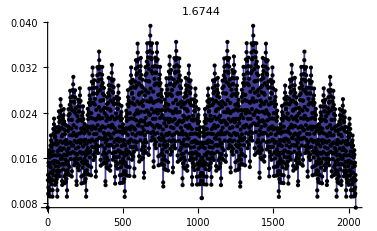

```mathematica
(* vecteurs propres *)
Block[{v=1.,r=.3,val,vp,i=11,vect=2,tt},
{val,vp}=Eigensystem[h[i]];
tt=Table[it,{it,2^i}];
ListPlot[vp[[vect]],Joined->True,PlotLabel->val[[vect]],Epilog->Point/@ MapThread[{#1,#2}&,{tt,vp[[vect]]}]]
]
```

```mathematica
(* hamiltonien avec conditions aux bords périodiques *)
Clear[hp];
hp[n_]:=Block[{tbl,ar},
tbl=Table[{i,i+1}->t[i],{i,1,2^n-1}];
(* clp *)
tbl=Join[tbl,{{1,2^n}->t[2^(n-1)]}];
ar=SparseArray[tbl,{2^n,2^n}];
(* Normal convertit en matrice *)
Normal[ar+Transpose[ar]]
]
hp[2]//MatrixForm
```

(0 | 1 | 0 | v
1 | 0 | v | 0
0 | v | 0 | 1
v | 0 | 1 | 0)

```mathematica
(* hamiltonien avec conditions aux bords antipériodiques *)
Clear[ha];
ha[n_]:=Block[{tbl,ar},
tbl=Table[{i,i+1}->t[i],{i,1,2^n-1}];
(* clp *)
tbl=Join[tbl,{{1,2^n}->-t[2^(n-1)]}];
ar=SparseArray[tbl,{2^n,2^n}];
(* Normal convertit en matrice *)
Normal[ar+Transpose[ar]]
]
ha[2]//MatrixForm
```

(0 | 1 | 0 | -v
1 | 0 | v | 0
0 | v | 0 | 1
-v | 0 | 1 | 0)

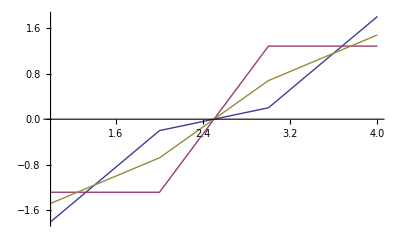

```mathematica
(* spectre *)
Block[{v=.8,r=0.3,vpp,vpa,vpn,i=2},
vpp=Sort[Eigenvalues[hp[i]]];
vpa=Sort[Eigenvalues[ha[i]]];
vpn=Sort[Eigenvalues[h[i]]];
(*Print[MapThread[(#1-#2)&,{vpp,vpa}]];*)
ListPlot[{vpp,vpa,vpn},Joined->True]
]
```

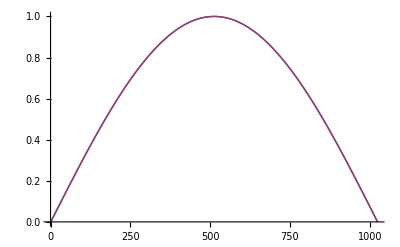

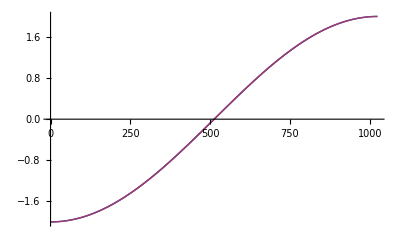

```mathematica
(* calcul des bandes effectives *)
Block[{v=1.,r=1.,vpp,vpa,bandlist,test,i=10},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i]]];
vpa=Sort[Eigenvalues[ha[i]]];
test = Table[Cos[k],{k,-Pi/2,Pi/2,Pi/(2^i-1)}];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
Print[ListPlot[{bandlist/bandlist[[Length@bandlist/2]],test},Joined->True]];
ListPlot[{vpp,vpa},Joined->True]
]
```

les spectres sont calculés !

-0.230845

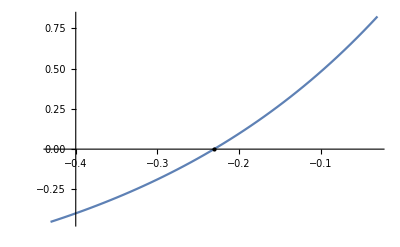

```mathematica
(* dimensions fractales en utilisant les bandes effectives comme largeur de boîte *)
Block[{v=1.,r=.1,vpp,vpa,vppN,vpaN,bandlist,bandlistN,i=11,gam,gamN,τ0},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i]]];
vpa=Sort[Eigenvalues[ha[i]]];
(* spectres des systèmes de taille i+1 p et anti-p *)
vppN=Sort[Eigenvalues[hp[i+1]]];
vpaN=Sort[Eigenvalues[ha[i+1]]];
Print["les spectres sont calculés !"];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandlistN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];
(* limite singulière quand r->1, r<1 !! *)
(*Print[ListPlot[bandlist,Joined->True]];*)
(* calcul des fonctions de partition Subscript[Γ, i] et Subscript[Γ, i+1] *)
gam=2^(-i q)Plus@@((bandlist)^-τ);
gamN=2^(-(i+1) q)Plus@@((bandlistN)^-τ);
(* Subscript[D, 0] *)
τ0=τ/.FindRoot[(gamN/gam/.q->0)-1,{τ,-1}];
Print[τ0];
(* vérif que FindRoot ne s'est pas planté *)
Print[Plot[(gamN/gam/.q->0)-1,{τ,τ0-0.2,τ0+0.2},Epilog->{PointSize[Medium],Point[{τ0,0}]}]]
(*ListPlot[{vpp,vpa},Joined->True]*)
]
```

```mathematica
(* dépendance en la taille du système *)
Clear[d0];
d0[i_,vv_,rr_]:=Block[{v=vv,r=rr,vpp,vpa,vppN,vpaN,bandlist,bandlistN,gam,gamN,τ0},
(* spectres des systèmes de taille i p et anti-p *)
vpp=Sort[Eigenvalues[hp[i]]];
vpa=Sort[Eigenvalues[ha[i]]];
(* spectres des systèmes de taille i+1 p et anti-p *)
vppN=Sort[Eigenvalues[hp[i+1]]];
vpaN=Sort[Eigenvalues[ha[i+1]]];
Print["Système de taille 2^n, n = ", i];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
bandlistN=MapThread[Abs[#1-#2]&,{vpaN,vppN}];
(* limite singulière quand r->1, r<1 !! *)
(*Print[ListPlot[bandlist,Joined->True]];*)
(* calcul des fonctions de partition Subscript[Γ, i] et Subscript[Γ, i+1] *)
gam=2^(-i q)Plus@@((bandlist)^-τ);
gamN=2^(-(i+1) q)Plus@@((bandlistN)^-τ);
(* Subscript[D, 0] *)
τ0=τ/.FindRoot[(gamN/gam/.q->0)-1,{τ,-1}];
τ0
]
```

```mathematica
d0[5,1.,.1]
```

Système de taille 2^n, n = 5

-0.231305

```mathematica
d0l=Table[d0[i,1.,.1],{i,2,11}]
```

Système de taille 2^n, n = 2

Système de taille 2^n, n = 3

Système de taille 2^n, n = 4

Système de taille 2^n, n = 5

Système de taille 2^n, n = 6

Système de taille 2^n, n = 7

Système de taille 2^n, n = 8

Système de taille 2^n, n = 9

Système de taille 2^n, n = 10

Système de taille 2^n, n = 11

{-0.23034,-0.23126,-0.231304,-0.231305,-0.231305,-0.231305,-0.231305,-0.231304,-0.23129,-0.230845}

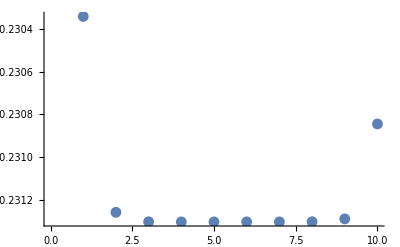

```mathematica
ListPlot[d0l]
```

```mathematica
d0l1=Table[d0[i,1.,1.],{i,2,11}]
```

Système de taille 2^n, n = 2

Système de taille 2^n, n = 3

Système de taille 2^n, n = 4

Système de taille 2^n, n = 5

Système de taille 2^n, n = 6

Système de taille 2^n, n = 7

Système de taille 2^n, n = 8

Système de taille 2^n, n = 9

Système de taille 2^n, n = 10

Système de taille 2^n, n = 11

{-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.}

```mathematica
(* dimension de Hausdorff par box-counting direct *)
Block[{v=1.,r=.1,i=10,spec,vp,b,δ=8,n=6,weight,weights={}},
(* spectre du système avec conditions aux limites nulles *)
spec=Sort[Eigenvalues[h[i]]];
(* normalisation du spectre : intervalle de longueur 1 centré sur 0 *)
spec=(spec-spec[[1]])/Abs[spec[[1]]-spec[[-1]]];
(*Print[ListPlot[spec]];*)
b=δ^-n;
vp=spec[[1]];
While[b≤1,
weight=0;
While[vp≤b,weight++;If[Length[spec]>1,spec=Rest[spec],Break[]];vp=spec[[1]]];
If[weight>0,AppendTo[weights,weight]];
b+=δ^-n;];
Print[Log[Length[weights]]/(n Log[δ])//N];
]
```

Eigenvalues::arh: Because finding 1024 out of the 1024 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

0.313548

```mathematica
(* dimensions fractales par box-counting direct *)
Clear[dDir];
dDir[q_?NumberQ,n_,δ_,i_]:=Block[{v=1.,r=.1,spec,vp,b,weight,weights={}},
(* spectre du système avec conditions aux limites nulles *)
spec=Sort[Eigenvalues[h[i]]];
(* normalisation du spectre : intervalle de longueur 1 centré sur 0 *)
spec=(spec-spec[[1]])/Abs[spec[[1]]-spec[[-1]]];
(*Print[ListPlot[spec]];*)
b=δ^-n;
vp=spec[[1]];
While[b≤1,
weight=0;
While[vp≤b,weight++;If[Length[spec]>1,spec=Rest[spec],Break[]];vp=spec[[1]]];
If[weight>0,AppendTo[weights,weight]];
b+=δ^-n;];
If[q==0,Return[Log[Length[weights]]/(n Log[δ])//N],Return[Log[Total[N[weights^q]]]/(n Log[δ])]];
]
```

```mathematica
dDir[0,6,8,10]
```

Eigenvalues::arh: Because finding 1024 out of the 1024 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

0.313548

```mathematica
ClearAll[nlist,d0list];
nlist=Table[nn,{nn,1,10,.2}];
d0list=dDir[0,#,5,10]&/@ nlist
```

Eigenvalues::arh: Because finding 1024 out of the 1024 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

General::stop: Further output of Eigenvalues :: arh will be suppressed during this calculation.

{0.861353,0.568838,0.615252,0.625,0.47853,0.556641,0.454545,0.416667,0.428186,0.397601,0.430677,0.426629,0.355606,0.358897,0.359266,0.38599,0.379451,0.362203,0.365784,0.341612,0.359178,0.338534,0.338793,0.320694,0.340454,0.329106,0.337455,0.326909,0.32627,0.32994,0.320513,0.316153,0.311807,0.314767,0.316267,0.315362,0.303646,0.302852,0.303782,0.303894,0.304228,0.295946,0.29443,0.296086,0.298018,0.294819}

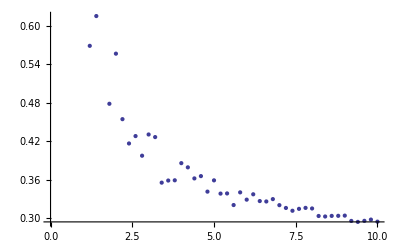

```mathematica
ListPlot[MapThread[{#1,#2}&,{nlist,d0list}]]
```

```mathematica
(* dimensions fractales des fonctions d'onde *)
dWF[q_?NumberQ,i_]:=Block[{v=1.,r=.1,chi,chiN,vec,vecN},
vec=Eigenvectors[h[i]][[2]];
vecN=Eigenvectors[h[i+1]][[2]];
chi=Plus@@((vec)^(2q));
chiN=Plus@@((vecN)^(2q));
(* τ(q) *)
Return[-Log2[chiN/chi]];
]
```

```mathematica
dWF[2,10]
```

Eigenvectors::arh: Because finding 1024 out of the 1024 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvectors.

Eigenvectors::arh: Because finding 2048 out of the 2048 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvectors.

0.996794